1000000000000000000000000

1.×10^22

100000000000000

1/1000000000000000000

1/100000000000000000000000000000000000000

1/100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

1000000000000000000000000000000

100

1.×10^-11

15

0

50

100000000

1-3/50 ⅇ^(-3/(10000000000000 √2))

1/1000000000000000000000000

(2 ϕ_0'[x])/x+ϕ_0''[x]==1000000000000000000000000000000000000000000000000 ((-1/10000000000000000000000000000000000000000000000000000000000000000000000000000+5.×10^-47 (1+Tanh[10 (1-x)])) ϕ_0[x]+ϕ_0[x]^3/10000000000000000000000000000000000000000000000000000000000000000000000000000)

{{ϕ_0[x]→InterpolatingFunction[…][x]}}

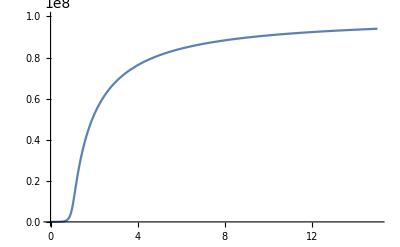

InterpolatingFunction::dmval: Input value {15.625} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {16.6667} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{δϕ[x,τ]→InterpolatingFunction[…][x,τ]}}

-Graphics3D-

(4000000000000000000000000000000000000000000000000000000 π)/3

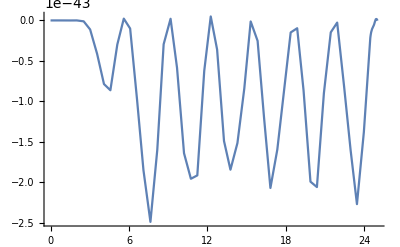

```mathematica
Subscript[R, c]=10^24
Subscript[ΔR, c]=0.01*Subscript[R, c]
Subscript[M, s]=1*10^14
Subscript[ρ, c]=10^-18
μ= 10^-38
λ=10^-92

K = Subscript[ρ, c]/(Subscript[M, s]^2*μ^2)
α =( Subscript[ρ, c]*Subscript[R, c]^2)/Subscript[M, s]^2
Subscript[x, min] = 0.00000000001
Subscript[x, max] = 15
Subscript[τ, min] = 0
Subscript[τ, max] = 50
Subscript[ϕ, ∞]=μ/Sqrt[λ]
(*Subscript[ϕ, 15]=1-(α/3)*(1/Subscript[x, max])*Exp[-Sqrt[2]*μ*Subscript[R, c]*Subscript[x, max]]*)
Subscript[ϕ, 15]=(-1+1/Sqrt[α])*(1/Subscript[x, max])*Exp[-Sqrt[2]*μ*Subscript[R, c]*Subscript[x, max]]+1
ω=1/Subscript[R, c]
θ[x_]:= 0.5*(Tanh[x*10]+1)
Subscript[ρ, 0][x_]:=Subscript[ρ, c]*θ[1-x]
ρ[x_,τ_] :=Subscript[ρ, 0][x]*(1+3(Subscript[ΔR, c]/Subscript[R, c])Sin[(ω*Subscript[R, c]*τ)])


ode = Subscript[ϕ, 0]''[x]+(2/x)*Subscript[ϕ, 0]'[x]== Subscript[R, c]^2*(((Subscript[ρ, 0][x]/Subscript[M, s]^2)-μ^2)*Subscript[ϕ, 0][x]+λ*Subscript[ϕ, ∞]^2*Subscript[ϕ, 0][x]^3)
sol1 = NDSolve[{ode,Subscript[ϕ, 0]'[Subscript[x, min]]==0,Subscript[ϕ, 0][Subscript[x, max]]== Subscript[ϕ, 15]},Subscript[ϕ, 0][x],{x,Subscript[x, min],Subscript[x, max]}]
Plot[Subscript[ϕ, ∞]*(Subscript[ϕ, 0][x]/.sol1),{x,0,15},PlotRange->{0,Subscript[ϕ, ∞]}]
f[x_,τ_]:= Subscript[R, c]^2*( ((Subscript[ρ, 0][x]/Subscript[M, s]^2)-μ^2)+3*μ^2*(Subscript[ϕ, 0][x]/.sol1)^2 )
δ[x_,τ_]:= Subscript[R, c]^2*(Subscript[ρ, 0][x]*3(Subscript[ΔR, c]/Subscript[R, c])Sin[(ω*Subscript[R, c]*τ)]/Subscript[M, s]^2)*Subscript[ϕ, 0][x]/.sol1

sol2 = NDSolve[{ -D[δϕ[x,τ],{τ,2}]+D[δϕ[x,τ],{x,2}]+(2/x)*D[δϕ[x,τ],{x,1}]-δ[x,τ]- f[x,τ]*δϕ[x,τ]==0,Derivative[0,1][δϕ][x,0]==0,δϕ[x,0]==0,δϕ[Subscript[x, min],τ]==0,δϕ[Subscript[x, max]+10,τ]==0},δϕ[x,τ],{x,Subscript[x, min],Subscript[x, max]+10},{τ,Subscript[τ, min],Subscript[τ, max]}]
Plot3D[δϕ[x,τ]/.sol2,{x,Subscript[x, min],Subscript[x, max]},{τ,Subscript[τ, min],Subscript[τ, max]},PlotRange->All]

Subscript[F, 0][x_] := Evaluate[Subscript[ϕ, 0][x]/.sol1]
F[x_,τ_] := Evaluate[δϕ[x,τ]/.sol2]
Subscript[F, r][x_,τ_] := Derivative[1,0][F][x,τ]
Subscript[F, t][x_,τ_] := Derivative[0,1][F][x,τ]

φ[x_,τ_] := Subscript[ϕ, ∞]*(Subscript[F, 0][x]+ F[x,τ])
Subscript[φ, r][x_,τ_] := Derivative[1,0][φ][x,τ]
Subscript[φ, t][x_,τ_] := Derivative[0,1][φ][x,τ]

plots=Table[Plot[φ[x,τ],{x,Subscript[x, min],Subscript[x, max]},PlotRange->{0,Subscript[ϕ, ∞]}],{τ,0,25,.25}];
ListAnimate[plots] 


P[τ_] := 4π*(5)^2*Subscript[ϕ, ∞]^2*Subscript[F, t][5,τ]*Subscript[F, r][5,τ]
Energy = (4/3)*π*Subscript[R, c]^3*Subscript[ρ, c]
Plot[P[τ]/Energy,{τ,0,25}]
```

```mathematica
Static = Table[{x,Subscript[F, 0][x]},{x,Subscript[x, min],Subscript[x, max]+0.1,0.1}]
Export["Static.txt",Static]
(*FilePrint["Static.txt"]*)

Subscript[P, 1] = Table[{x,F[x,6]},{x,Subscript[x, min],Subscript[x, max]+0.1,0.1}]
Export["P_t=6.txt",Subscript[P, 1]]
(*FilePrint["Static.txt"]*)

Subscript[P, 2] = Table[{τ,F[1,τ]},{τ,Subscript[τ, min],Subscript[τ, max],0.1}]
Export["P_x=1.txt",Subscript[P, 2]]

Subscript[P, 3] = Table[{τ,F[5,τ]},{τ,Subscript[τ, min],Subscript[τ, max],0.1}]
Export["P_x=5.txt",Subscript[P, 3]]

Pw = Table[{τ,10^(43)P[τ]/Energy},{τ,Subscript[τ, min],25,0.1}]
Export["Power.txt",Pw]
```

{{1.×10^-11,{0.0000716258}},{0.1,{0.0000841796}},{0.2,{0.0001299}},{0.3,{0.000239211}},{0.4,{0.000488739}},{0.5,{0.00106313}},{0.6,{0.00240826}},{0.7,{0.00560967}},{0.8,{0.0133164}},{0.9,{0.0317294}},{1.,{0.0715186}},{1.1,{0.133855}},{1.2,{0.201054}},{1.3,{0.261875}},{1.4,{0.314759}},{1.5,{0.360719}},{1.6,{0.400953}},{1.7,{0.436457}},{1.8,{0.468017}},{1.9,{0.496255}},{2.,{0.521669}},{2.1,{0.544662}},{2.2,{0.565565}},{2.3,{0.584651}},{2.4,{0.602146}},{2.5,{0.618241}},{2.6,{0.633099}},{2.7,{0.646856}},{2.8,{0.65963}},{2.9,{0.671523}},{3.,{0.682623}},{3.1,{0.693007}},{3.2,{0.702743}},{3.3,{0.711888}},{3.4,{0.720495}},{3.5,{0.72861}},{3.6,{0.736275}},{3.7,{0.743525}},{3.8,{0.750394}},{3.9,{0.75691}},{4.,{0.763101}},{4.1,{0.768989}},{4.2,{0.774597}},{4.3,{0.779945}},{4.4,{0.785049}},{4.5,{0.789926}},{4.6,{0.794592}},{4.7,{0.799059}},{4.8,{0.803339}},{4.9,{0.807445}},{5.,{0.811387}},{5.1,{0.815174}},{5.2,{0.818816}},{5.3,{0.82232}},{5.4,{0.825694}},{5.5,{0.828946}},{5.6,{0.832081}},{5.7,{0.835107}},{5.8,{0.838028}},{5.9,{0.84085}},{6.,{0.843578}},{6.1,{0.846217}},{6.2,{0.84877}},{6.3,{0.851243}},{6.4,{0.853638}},{6.5,{0.855959}},{6.6,{0.85821}},{6.7,{0.860394}},{6.8,{0.862514}},{6.9,{0.864572}},{7.,{0.866572}},{7.1,{0.868515}},{7.2,{0.870404}},{7.3,{0.872241}},{7.4,{0.874029}},{7.5,{0.875769}},{7.6,{0.877463}},{7.7,{0.879114}},{7.8,{0.880721}},{7.9,{0.882289}},{8.,{0.883817}},{8.1,{0.885307}},{8.2,{0.886761}},{8.3,{0.88818}},{8.4,{0.889565}},{8.5,{0.890918}},{8.6,{0.892239}},{8.7,{0.89353}},{8.8,{0.894791}},{8.9,{0.896024}},{9.,{0.89723}},{9.1,{0.898409}},{9.2,{0.899562}},{9.3,{0.900691}},{9.4,{0.901796}},{9.5,{0.902877}},{9.6,{0.903936}},{9.7,{0.904973}},{9.8,{0.905989}},{9.9,{0.906984}},{10.,{0.90796}},{10.1,{0.908916}},{10.2,{0.909854}},{10.3,{0.910773}},{10.4,{0.911674}},{10.5,{0.912559}},{10.6,{0.913426}},{10.7,{0.914278}},{10.8,{0.915113}},{10.9,{0.915934}},{11.,{0.916739}},{11.1,{0.91753}},{11.2,{0.918307}},{11.3,{0.91907}},{11.4,{0.91982}},{11.5,{0.920556}},{11.6,{0.92128}},{11.7,{0.921992}},{11.8,{0.922691}},{11.9,{0.923379}},{12.,{0.924055}},{12.1,{0.924721}},{12.2,{0.925375}},{12.3,{0.926018}},{12.4,{0.926651}},{12.5,{0.927275}},{12.6,{0.927888}},{12.7,{0.928491}},{12.8,{0.929085}},{12.9,{0.92967}},{13.,{0.930246}},{13.1,{0.930813}},{13.2,{0.931372}},{13.3,{0.931922}},{13.4,{0.932464}},{13.5,{0.932997}},{13.6,{0.933523}},{13.7,{0.934042}},{13.8,{0.934552}},{13.9,{0.935056}},{14.,{0.935552}},{14.1,{0.936041}},{14.2,{0.936524}},{14.3,{0.936999}},{14.4,{0.937468}},{14.5,{0.937931}},{14.6,{0.938387}},{14.7,{0.938837}},{14.8,{0.939281}},{14.9,{0.939719}},{15.,{0.940151}}}

Static.txt

{{1.×10^-11,{0.}},{0.1,{-0.0000465721}},{0.2,{-0.0000412408}},{0.3,{6.50256×10^-6}},{0.4,{0.0000879882}},{0.5,{0.000195338}},{0.6,{0.000321433}},{0.7,{0.000459887}},{0.8,{0.000605009}},{0.9,{0.000751782}},{1.,{0.000895821}},{1.1,{0.00103335}},{1.2,{0.00116118}},{1.3,{0.00127665}},{1.4,{0.00137762}},{1.5,{0.00146245}},{1.6,{0.00152994}},{1.7,{0.0015793}},{1.8,{0.00161017}},{1.9,{0.00162251}},{2.,{0.00161665}},{2.1,{0.00159319}},{2.2,{0.00155302}},{2.3,{0.00149726}},{2.4,{0.00142723}},{2.5,{0.00134446}},{2.6,{0.00125059}},{2.7,{0.0011474}},{2.8,{0.00103675}},{2.9,{0.000920551}},{3.,{0.000800749}},{3.1,{0.000679276}},{3.2,{0.000566699}},{3.3,{0.000458487}},{3.4,{0.00035269}},{3.5,{0.000250188}},{3.6,{0.000151782}},{3.7,{0.0000581975}},{3.8,{-0.0000299227}},{3.9,{-0.000112015}},{4.,{-0.000187597}},{4.1,{-0.000256269}},{4.2,{-0.000316666}},{4.3,{-0.000367591}},{4.4,{-0.000411198}},{4.5,{-0.000447632}},{4.6,{-0.000477107}},{4.7,{-0.000499896}},{4.8,{-0.00051633}},{4.9,{-0.000526786}},{5.,{-0.000531681}},{5.1,{-0.000531469}},{5.2,{-0.000526627}},{5.3,{-0.000518823}},{5.4,{-0.000507427}},{5.5,{-0.000492761}},{5.6,{-0.000475265}},{5.7,{-0.000455374}},{5.8,{-0.000433526}},{5.9,{-0.000410149}},{6.,{-0.000385663}},{6.1,{-0.000360474}},{6.2,{-0.000334971}},{6.3,{-0.000310493}},{6.4,{-0.000287315}},{6.5,{-0.000264647}},{6.6,{-0.000242647}},{6.7,{-0.000221449}},{6.8,{-0.000201164}},{6.9,{-0.000181881}},{7.,{-0.000163671}},{7.1,{-0.000146586}},{7.2,{-0.00013066}},{7.3,{-0.000115913}},{7.4,{-0.000102383}},{7.5,{-0.0000900179}},{7.6,{-0.0000787916}},{7.7,{-0.0000686668}},{7.8,{-0.0000595965}},{7.9,{-0.0000515252}},{8.,{-0.0000443905}},{8.1,{-0.000038124}},{8.2,{-0.0000326532}},{8.3,{-0.0000279024}},{8.4,{-0.0000235064}},{8.5,{-0.0000195506}},{8.6,{-0.0000161319}},{8.7,{-0.000013203}},{8.8,{-0.0000107175}},{8.9,{-8.62985×10^-6}},{9.,{-6.89555×10^-6}},{9.1,{-5.47166×10^-6}},{9.2,{-4.3168×10^-6}},{9.3,{-3.39147×10^-6}},{9.4,{-2.62274×10^-6}},{9.5,{-1.9075×10^-6}},{9.6,{-1.32899×10^-6}},{9.7,{-8.66759×10^-7}},{9.8,{-5.02574×10^-7}},{9.9,{-2.20287×10^-7}},{10.,{-5.71281×10^-9}},{10.1,{1.53503×10^-7}},{10.2,{2.68012×10^-7}},{10.3,{3.46896×10^-7}},{10.4,{3.97792×10^-7}},{10.5,{4.12978×10^-7}},{10.6,{4.09777×10^-7}},{10.7,{3.96235×10^-7}},{10.8,{3.7656×10^-7}},{10.9,{3.5404×10^-7}},{11.,{3.31129×10^-7}},{11.1,{3.09537×10^-7}},{11.2,{2.90308×10^-7}},{11.3,{2.73913×10^-7}},{11.4,{2.60332×10^-7}},{11.5,{2.38923×10^-7}},{11.6,{2.05589×10^-7}},{11.7,{1.75303×10^-7}},{11.8,{1.48524×10^-7}},{11.9,{1.25499×10^-7}},{12.,{1.06287×10^-7}},{12.1,{9.07822×10^-8}},{12.2,{7.87392×10^-8}},{12.3,{6.97939×10^-8}},{12.4,{6.34883×10^-8}},{12.5,{5.92933×10^-8}},{12.6,{4.86739×10^-8}},{12.7,{3.95388×10^-8}},{12.8,{3.18168×10^-8}},{12.9,{2.54183×10^-8}},{13.,{2.02378×10^-8}},{13.1,{1.61572×10^-8}},{13.2,{1.30479×10^-8}},{13.3,{1.07744×10^-8}},{13.4,{9.19661×10^-9}},{13.5,{8.17298×10^-9}},{13.6,{6.85592×10^-9}},{13.7,{5.35917×10^-9}},{13.8,{4.14157×10^-9}},{13.9,{3.16069×10^-9}},{14.,{2.3787×10^-9}},{14.1,{1.76214×10^-9}},{14.2,{1.28161×10^-9}},{14.3,{9.11577×10^-10}},{14.4,{6.3003×10^-10}},{14.5,{4.18274×10^-10}},{14.6,{2.65104×10^-10}},{14.7,{1.74983×10^-10}},{14.8,{1.13567×10^-10}},{14.9,{7.09609×10^-11}},{15.,{3.93953×10^-11}}}

P_t=6.txt

{{0.,{0.}},{0.1,{-0.000142301}},{0.2,{-0.000315239}},{0.3,{-0.000583704}},{0.4,{-0.000901592}},{0.5,{-0.00124961}},{0.6,{-0.00158378}},{0.7,{-0.00187818}},{0.8,{-0.00213157}},{0.9,{-0.00233145}},{1.,{-0.00246802}},{1.1,{-0.002559}},{1.2,{-0.00261269}},{1.3,{-0.00264331}},{1.4,{-0.00266485}},{1.5,{-0.00269111}},{1.6,{-0.00272517}},{1.7,{-0.00275458}},{1.8,{-0.00274926}},{1.9,{-0.00272676}},{2.,{-0.00263881}},{2.1,{-0.00253371}},{2.2,{-0.00238945}},{2.3,{-0.00220567}},{2.4,{-0.00199481}},{2.5,{-0.00176721}},{2.6,{-0.00150585}},{2.7,{-0.00123523}},{2.8,{-0.000975443}},{2.9,{-0.000695238}},{3.,{-0.00041032}},{3.1,{-0.000141774}},{3.2,{0.000130482}},{3.3,{0.000404452}},{3.4,{0.000666525}},{3.5,{0.000919669}},{3.6,{0.00117009}},{3.7,{0.00142047}},{3.8,{0.00166164}},{3.9,{0.00187515}},{4.,{0.00206373}},{4.1,{0.00224211}},{4.2,{0.00241659}},{4.3,{0.00256775}},{4.4,{0.00267472}},{4.5,{0.00274527}},{4.6,{0.00279741}},{4.7,{0.00283528}},{4.8,{0.00284184}},{4.9,{0.00281316}},{5.,{0.00275154}},{5.1,{0.00266063}},{5.2,{0.00254385}},{5.3,{0.00240298}},{5.4,{0.00223663}},{5.5,{0.00204427}},{5.6,{0.00183984}},{5.7,{0.00162912}},{5.8,{0.00140746}},{5.9,{0.00116565}},{6.,{0.000895821}},{6.1,{0.000597332}},{6.2,{0.000284306}},{6.3,{-0.0000115598}},{6.4,{-0.000277418}},{6.5,{-0.000522943}},{6.6,{-0.000768263}},{6.7,{-0.00103183}},{6.8,{-0.0013183}},{6.9,{-0.00160676}},{7.,{-0.00185882}},{7.1,{-0.00205845}},{7.2,{-0.00221417}},{7.3,{-0.00234678}},{7.4,{-0.00247701}},{7.5,{-0.00261318}},{7.6,{-0.00273919}},{7.7,{-0.00282575}},{7.8,{-0.00286366}},{7.9,{-0.00285747}},{8.,{-0.00281852}},{8.1,{-0.00275861}},{8.2,{-0.00268377}},{8.3,{-0.00258804}},{8.4,{-0.00246252}},{8.5,{-0.00231433}},{8.6,{-0.00214651}},{8.7,{-0.0019573}},{8.8,{-0.00174295}},{8.9,{-0.00150059}},{9.,{-0.00123105}},{9.1,{-0.000946892}},{9.2,{-0.000673772}},{9.3,{-0.000417614}},{9.4,{-0.000167323}},{9.5,{0.000094742}},{9.6,{0.000382297}},{9.7,{0.000694658}},{9.8,{0.00100669}},{9.9,{0.0012823}},{10.,{0.00151155}},{10.1,{0.00170726}},{10.2,{0.00189204}},{10.3,{0.00208534}},{10.4,{0.0022905}},{10.5,{0.00248336}},{10.6,{0.00263193}},{10.7,{0.00272756}},{10.8,{0.00277866}},{10.9,{0.00280164}},{11.,{0.00281176}},{11.1,{0.00281414}},{11.2,{0.00279555}},{11.3,{0.00274168}},{11.4,{0.00265415}},{11.5,{0.00253608}},{11.6,{0.00239045}},{11.7,{0.00221946}},{11.8,{0.00202385}},{11.9,{0.00180238}},{12.,{0.00156386}},{12.1,{0.00132609}},{12.2,{0.00109053}},{12.3,{0.000847312}},{12.4,{0.000583273}},{12.5,{0.000290039}},{12.6,{-0.0000279336}},{12.7,{-0.000344228}},{12.8,{-0.000627939}},{12.9,{-0.000875347}},{13.,{-0.00110217}},{13.1,{-0.00133079}},{13.2,{-0.00157742}},{13.3,{-0.00183936}},{13.4,{-0.00208569}},{13.5,{-0.00228448}},{13.6,{-0.00243029}},{13.7,{-0.00253619}},{13.8,{-0.00262259}},{13.9,{-0.00270601}},{14.,{-0.00278785}},{14.1,{-0.00284631}},{14.2,{-0.00286291}},{14.3,{-0.00283652}},{14.4,{-0.00277295}},{14.5,{-0.00268075}},{14.6,{-0.00256713}},{14.7,{-0.00243391}},{14.8,{-0.00227468}},{14.9,{-0.00209346}},{15.,{-0.00190057}},{15.1,{-0.00169582}},{15.2,{-0.00147278}},{15.3,{-0.00122389}},{15.4,{-0.000945495}},{15.5,{-0.000643166}},{15.6,{-0.000341974}},{15.7,{-0.0000652539}},{15.8,{0.000188447}},{15.9,{0.000435631}},{16.,{0.000696141}},{16.1,{0.000981451}},{16.2,{0.00128295}},{16.3,{0.00156572}},{16.4,{0.00180096}},{16.5,{0.00198809}},{16.6,{0.00214438}},{16.7,{0.00229237}},{16.8,{0.00244732}},{16.9,{0.00260464}},{17.,{0.00273453}},{17.1,{0.00281631}},{17.2,{0.00284919}},{17.3,{0.00284331}},{17.4,{0.0028126}},{17.5,{0.00276753}},{17.6,{0.00270795}},{17.7,{0.00262017}},{17.8,{0.00250318}},{17.9,{0.00236185}},{18.,{0.00219715}},{18.1,{0.00200774}},{18.2,{0.00179175}},{18.3,{0.00154847}},{18.4,{0.00128149}},{18.5,{0.00101217}},{18.6,{0.000755651}},{18.7,{0.000507366}},{18.8,{0.000252406}},{18.9,{-0.0000246955}},{19.,{-0.000330173}},{19.1,{-0.000651116}},{19.2,{-0.000951763}},{19.3,{-0.00120916}},{19.4,{-0.00142789}},{19.5,{-0.00162791}},{19.6,{-0.00183162}},{19.7,{-0.00205076}},{19.8,{-0.00227347}},{19.9,{-0.00246434}},{20.,{-0.00260284}},{20.1,{-0.00269115}},{20.2,{-0.00274433}},{20.3,{-0.00278045}},{20.4,{-0.00281087}},{20.5,{-0.00283035}},{20.6,{-0.00281764}},{20.7,{-0.00276718}},{20.8,{-0.00268152}},{20.9,{-0.00256508}},{21.,{-0.00242234}},{21.1,{-0.00225615}},{21.2,{-0.00206598}},{21.3,{-0.00185079}},{21.4,{-0.00162649}},{21.5,{-0.00140123}},{21.6,{-0.00116993}},{21.7,{-0.000921407}},{21.8,{-0.000645623}},{21.9,{-0.000340815}},{22.,{-0.0000215769}},{22.1,{0.000278687}},{22.2,{0.000544395}},{22.3,{0.000784233}},{22.4,{0.00101879}},{22.5,{0.00126798}},{22.6,{0.00153854}},{22.7,{0.00181169}},{22.8,{0.00204941}},{22.9,{0.0022341}},{23.,{0.00237243}},{23.1,{0.00248374}},{23.2,{0.00258834}},{23.3,{0.00269579}},{23.4,{0.00279337}},{23.5,{0.00285373}},{23.6,{0.00286814}},{23.7,{0.00284008}},{23.8,{0.00277882}},{23.9,{0.00269438}},{24.,{0.00259239}},{24.1,{0.00246904}},{24.2,{0.00231757}},{24.3,{0.00214742}},{24.4,{0.00196242}},{24.5,{0.0017595}},{24.6,{0.00153279}},{24.7,{0.00127763}},{24.8,{0.000994692}},{24.9,{0.000697429}},{25.,{0.000414077}},{25.1,{0.000152981}},{25.2,{-0.0000967126}},{25.3,{-0.000353863}},{25.4,{-0.000634131}},{25.5,{-0.000938778}},{25.6,{-0.00124397}},{25.7,{-0.00151239}},{25.8,{-0.0017317}},{25.9,{-0.00191316}},{26.,{-0.00207888}},{26.1,{-0.00224903}},{26.2,{-0.00242903}},{26.3,{-0.00259782}},{26.4,{-0.00272411}},{26.5,{-0.00279865}},{26.6,{-0.00282822}},{26.7,{-0.00282733}},{26.8,{-0.0028102}},{26.9,{-0.00278264}},{27.,{-0.00273447}},{27.1,{-0.00265329}},{27.2,{-0.00254252}},{27.3,{-0.0024049}},{27.4,{-0.00224146}},{27.5,{-0.00205221}},{27.6,{-0.00183679}},{27.7,{-0.00159514}},{27.8,{-0.00133759}},{27.9,{-0.00108502}},{28.,{-0.000840321}},{28.1,{-0.000592876}},{28.2,{-0.000327646}},{28.3,{-0.0000342099}},{28.4,{0.00028418}},{28.5,{0.000601317}},{28.6,{0.000883919}},{28.7,{0.0011259}},{28.8,{0.00134207}},{28.9,{0.00155519}},{29.,{0.00178296}},{29.1,{0.00202509}},{29.2,{0.00225298}},{29.3,{0.00243429}},{29.4,{0.00256203}},{29.5,{0.00264749}},{29.6,{0.00270973}},{29.7,{0.00276509}},{29.8,{0.00281675}},{29.9,{0.00284623}},{30.,{0.00283641}},{30.1,{0.00278684}},{30.2,{0.00270204}},{30.3,{0.0025884}},{30.4,{0.0024514}},{30.5,{0.00229277}},{30.6,{0.00210842}},{30.7,{0.00190425}},{30.8,{0.00169328}},{30.9,{0.00147563}},{31.,{0.00124332}},{31.1,{0.000986582}},{31.2,{0.000700097}},{31.3,{0.000389345}},{31.4,{0.0000801899}},{31.5,{-0.000200931}},{31.6,{-0.000453662}},{31.7,{-0.00069447}},{31.8,{-0.000944418}},{31.9,{-0.00121694}},{32.,{-0.0015056}},{32.1,{-0.00177666}},{32.2,{-0.00199975}},{32.3,{-0.00217228}},{32.4,{-0.00231003}},{32.5,{-0.00243498}},{32.6,{-0.00256317}},{32.7,{-0.00269256}},{32.8,{-0.00279623}},{32.9,{-0.00285405}},{33.,{-0.00286473}},{33.1,{-0.00283661}},{33.2,{-0.00278165}},{33.3,{-0.00270935}},{33.4,{-0.0026207}},{33.5,{-0.00250496}},{33.6,{-0.00236297}},{33.7,{-0.00220137}},{33.8,{-0.00202039}},{33.9,{-0.0018166}},{34.,{-0.00158602}},{34.1,{-0.00132709}},{34.2,{-0.0010445}},{34.3,{-0.000761236}},{34.4,{-0.000495556}},{34.5,{-0.000243825}},{34.6,{9.7399×10^-6}},{34.7,{0.000282457}},{34.8,{0.000582562}},{34.9,{0.000898558}},{35.,{0.00119464}},{35.1,{0.00144532}},{35.2,{0.00165323}},{35.3,{0.00183753}},{35.4,{0.00202092}},{35.5,{0.00221676}},{35.6,{0.00241606}},{35.7,{0.00258522}},{35.8,{0.00270331}},{35.9,{0.00277109}},{36.,{0.00280175}},{36.1,{0.00281198}},{36.2,{0.0028131}},{36.3,{0.00280221}},{36.4,{0.00276085}},{36.5,{0.00268505}},{36.6,{0.00257786}},{36.7,{0.00244215}},{36.8,{0.00228017}},{36.9,{0.00209315}},{37.,{0.00188087}},{37.1,{0.00164428}},{37.2,{0.00140151}},{37.3,{0.00116315}},{37.4,{0.000924025}},{37.5,{0.000671319}},{37.6,{0.00039285}},{37.7,{0.0000853046}},{37.8,{-0.000237058}},{37.9,{-0.000539585}},{38.,{-0.000803759}},{38.1,{-0.00103685}},{38.2,{-0.00125949}},{38.3,{-0.00149277}},{38.4,{-0.0017455}},{38.5,{-0.00200145}},{38.6,{-0.00222319}},{38.7,{-0.00239166}},{38.8,{-0.0025117}},{38.9,{-0.00260112}},{39.,{-0.00267968}},{39.1,{-0.00275792}},{39.2,{-0.00282623}},{39.3,{-0.00285936}},{39.4,{-0.00284948}},{39.5,{-0.00279939}},{39.6,{-0.00271639}},{39.7,{-0.0026085}},{39.8,{-0.00248056}},{39.9,{-0.00233046}},{40.,{-0.00215361}},{40.1,{-0.00196198}},{40.2,{-0.00176068}},{40.3,{-0.00154561}},{40.4,{-0.00130874}},{40.5,{-0.00104344}},{40.6,{-0.000749741}},{40.7,{-0.000441807}},{40.8,{-0.000150143}},{40.9,{0.000114229}},{41.,{0.000361582}},{41.1,{0.000611697}},{41.2,{0.000882044}},{41.3,{0.00117596}},{41.4,{0.00147131}},{41.5,{0.00173008}},{41.6,{0.0019377}},{41.7,{0.00210369}},{41.8,{0.00224934}},{41.9,{0.00239517}},{42.,{0.00254844}},{42.1,{0.00269131}},{42.2,{0.00279368}},{42.3,{0.00284612}},{42.4,{0.00285392}},{42.5,{0.00282961}},{42.6,{0.00278603}},{42.7,{0.00272926}},{42.8,{0.00265189}},{42.9,{0.00254358}},{43.,{0.00240987}},{43.1,{0.00225354}},{43.2,{0.00207387}},{43.3,{0.00186862}},{43.4,{0.00163599}},{43.5,{0.0013766}},{43.6,{0.00110211}},{43.7,{0.000836413}},{43.8,{0.00058421}},{43.9,{0.000334524}},{44.,{0.0000706435}},{44.1,{-0.000219915}},{44.2,{-0.000535449}},{44.3,{-0.000850361}},{44.4,{-0.00112944}},{44.5,{-0.00136414}},{44.6,{-0.00156808}},{44.7,{-0.00176405}},{44.8,{-0.00197096}},{44.9,{-0.00219084}},{45.,{-0.00239782}},{45.1,{-0.00255957}},{45.2,{-0.0026679}},{45.3,{-0.00273229}},{45.4,{-0.00277021}},{45.5,{-0.00279747}},{45.6,{-0.00281863}},{45.7,{-0.0028185}},{45.8,{-0.00278158}},{45.9,{-0.00270857}},{46.,{-0.00260301}},{46.1,{-0.00246916}},{46.2,{-0.00231051}},{46.3,{-0.00212834}},{46.4,{-0.00192044}},{46.5,{-0.00169449}},{46.6,{-0.00146647}},{46.7,{-0.00123722}},{46.8,{-0.000997521}},{46.9,{-0.000735455}},{47.,{-0.000443837}},{47.1,{-0.000127609}},{47.2,{0.000186953}},{47.3,{0.000470503}},{47.4,{0.000720611}},{47.5,{0.000953361}},{47.6,{0.00119073}},{47.7,{0.00144797}},{47.8,{0.00172099}},{47.9,{0.00197771}},{48.,{0.00218657}},{48.1,{0.00234312}},{48.2,{0.00246146}},{48.3,{0.00256271}},{48.4,{0.00266334}},{48.5,{0.00276359}},{48.6,{0.00283968}},{48.7,{0.00287235}},{48.8,{0.00286024}},{48.9,{0.00281004}},{49.,{0.00273164}},{49.1,{0.00263324}},{49.2,{0.00251649}},{49.3,{0.00237346}},{49.4,{0.0022055}},{49.5,{0.00201463}},{49.6,{0.00179617}},{49.7,{0.00155657}},{49.8,{0.0013155}},{49.9,{0.00106413}},{50.,{0.000788085}}}

P_x=1.txt

{{0.,{0.}},{0.1,{-6.29097×10^-15}},{0.2,{2.18205×10^-9}},{0.3,{1.68859×10^-8}},{0.4,{4.95252×10^-8}},{0.5,{1.14932×10^-7}},{0.6,{2.20317×10^-7}},{0.7,{3.79828×10^-7}},{0.8,{5.84623×10^-7}},{0.9,{8.55506×10^-7}},{1.,{1.20478×10^-6}},{1.1,{1.63218×10^-6}},{1.2,{2.14096×10^-6}},{1.3,{2.72489×10^-6}},{1.4,{3.3708×10^-6}},{1.5,{4.05796×10^-6}},{1.6,{4.75376×10^-6}},{1.7,{5.40273×10^-6}},{1.8,{5.91619×10^-6}},{1.9,{6.27887×10^-6}},{2.,{6.31825×10^-6}},{2.1,{6.01534×10^-6}},{2.2,{5.13461×10^-6}},{2.3,{3.64951×10^-6}},{2.4,{1.047×10^-6}},{2.5,{-2.81687×10^-6}},{2.6,{-7.38029×10^-6}},{2.7,{-0.0000133937}},{2.8,{-0.0000213601}},{2.9,{-0.0000304509}},{3.,{-0.0000411581}},{3.1,{-0.0000542243}},{3.2,{-0.0000689363}},{3.3,{-0.000085336}},{3.4,{-0.000103814}},{3.5,{-0.000124247}},{3.6,{-0.000146497}},{3.7,{-0.000170524}},{3.8,{-0.000196183}},{3.9,{-0.00022244}},{4.,{-0.000249354}},{4.1,{-0.000277776}},{4.2,{-0.000308089}},{4.3,{-0.000338719}},{4.4,{-0.000367324}},{4.5,{-0.000394663}},{4.6,{-0.000422766}},{4.7,{-0.000452115}},{4.8,{-0.000479524}},{4.9,{-0.000501666}},{5.,{-0.0005183}},{5.1,{-0.000531206}},{5.2,{-0.0005428}},{5.3,{-0.000554743}},{5.4,{-0.000566555}},{5.5,{-0.000574818}},{5.6,{-0.000576612}},{5.7,{-0.000571643}},{5.8,{-0.000561268}},{5.9,{-0.000547444}},{6.,{-0.000531681}},{6.1,{-0.000513993}},{6.2,{-0.000492376}},{6.3,{-0.000466323}},{6.4,{-0.000436395}},{6.5,{-0.000402841}},{6.6,{-0.000365696}},{6.7,{-0.000324891}},{6.8,{-0.000280364}},{6.9,{-0.000232374}},{7.,{-0.000183802}},{7.1,{-0.000136944}},{7.2,{-0.0000912369}},{7.3,{-0.0000445825}},{7.4,{5.24346×10^-6}},{7.5,{0.0000591813}},{7.6,{0.000115453}},{7.7,{0.000168639}},{7.8,{0.000214947}},{7.9,{0.000254983}},{8.,{0.000291863}},{8.1,{0.000329141}},{8.2,{0.000368738}},{8.3,{0.000408872}},{8.4,{0.000443811}},{8.5,{0.000469948}},{8.6,{0.000487544}},{8.7,{0.000499102}},{8.8,{0.000507692}},{8.9,{0.000515279}},{9.,{0.000521048}},{9.1,{0.000521327}},{9.2,{0.000514903}},{9.3,{0.000502151}},{9.4,{0.000483901}},{9.5,{0.000461064}},{9.6,{0.000434242}},{9.7,{0.000403348}},{9.8,{0.000367984}},{9.9,{0.000330582}},{10.,{0.000292529}},{10.1,{0.000253078}},{10.2,{0.000210487}},{10.3,{0.000163154}},{10.4,{0.000110761}},{10.5,{0.00005557}},{10.6,{3.11846×10^-6}},{10.7,{-0.0000438505}},{10.8,{-0.0000867177}},{10.9,{-0.000128914}},{11.,{-0.000173807}},{11.1,{-0.00022259}},{11.2,{-0.000272204}},{11.3,{-0.000316114}},{11.4,{-0.000351119}},{11.5,{-0.000378297}},{11.6,{-0.000400986}},{11.7,{-0.000422745}},{11.8,{-0.000445299}},{11.9,{-0.000466518}},{12.,{-0.000481471}},{12.1,{-0.00048835}},{12.2,{-0.000487719}},{12.3,{-0.000481315}},{12.4,{-0.000471059}},{12.5,{-0.000458063}},{12.6,{-0.000441648}},{12.7,{-0.000420243}},{12.8,{-0.000395066}},{12.9,{-0.000366762}},{13.,{-0.000335022}},{13.1,{-0.000299119}},{13.2,{-0.000258449}},{13.3,{-0.000213068}},{13.4,{-0.000164835}},{13.5,{-0.000118224}},{13.6,{-0.0000746842}},{13.7,{-0.0000325552}},{13.8,{0.0000111468}},{13.9,{0.0000589403}},{14.,{0.00011109}},{14.1,{0.000163851}},{14.2,{0.000210981}},{14.3,{0.000250256}},{14.4,{0.000283493}},{14.5,{0.000314392}},{14.6,{0.000346378}},{14.7,{0.000380436}},{14.8,{0.00041309}},{14.9,{0.000438787}},{15.,{0.000455677}},{15.1,{0.000464902}},{15.2,{0.000469083}},{15.3,{0.000470831}},{15.4,{0.000471261}},{15.5,{0.000468564}},{15.6,{0.000460096}},{15.7,{0.000446021}},{15.8,{0.000426844}},{15.9,{0.000403041}},{16.,{0.000374965}},{16.1,{0.000342754}},{16.2,{0.000306243}},{16.3,{0.000266535}},{16.4,{0.000226763}},{16.5,{0.000187472}},{16.6,{0.000147164}},{16.7,{0.000103634}},{16.8,{0.0000553211}},{16.9,{2.64613×10^-6}},{17.,{-0.0000504615}},{17.1,{-0.0000985408}},{17.2,{-0.000140457}},{17.3,{-0.000178553}},{17.4,{-0.000216521}},{17.5,{-0.000257287}},{17.6,{-0.000300881}},{17.7,{-0.000342668}},{17.8,{-0.000376956}},{17.9,{-0.000402349}},{18.,{-0.000420757}},{18.1,{-0.000435522}},{18.2,{-0.000449563}},{18.3,{-0.00046351}},{18.4,{-0.000474126}},{18.5,{-0.00047793}},{18.6,{-0.000474508}},{18.7,{-0.000464728}},{18.8,{-0.000450007}},{18.9,{-0.000431618}},{19.,{-0.000410009}},{19.1,{-0.000384216}},{19.2,{-0.000354481}},{19.3,{-0.000322653}},{19.4,{-0.000288879}},{19.5,{-0.000252186}},{19.6,{-0.000211311}},{19.7,{-0.000165536}},{19.8,{-0.000115533}},{19.9,{-0.0000650424}},{20.,{-0.0000183557}},{20.1,{0.0000243425}},{20.2,{0.0000655972}},{20.3,{0.000108738}},{20.4,{0.000155936}},{20.5,{0.000206256}},{20.6,{0.000254281}},{20.7,{0.000294705}},{20.8,{0.000326936}},{20.9,{0.000353616}},{21.,{0.000378512}},{21.1,{0.000404424}},{21.2,{0.000431088}},{21.3,{0.000453848}},{21.4,{0.000468759}},{21.5,{0.000475379}},{21.6,{0.000475261}},{21.7,{0.000470735}},{21.8,{0.000463698}},{21.9,{0.000454399}},{22.,{0.000440665}},{22.1,{0.000421891}},{22.2,{0.000398944}},{22.3,{0.000372059}},{22.4,{0.000341066}},{22.5,{0.000305672}},{22.6,{0.000265727}},{22.7,{0.000221633}},{22.8,{0.000176597}},{22.9,{0.000133549}},{23.,{0.000092043}},{23.1,{0.0000497227}},{23.2,{3.94375×10^-6}},{23.3,{-0.0000465953}},{23.4,{-0.000100216}},{23.5,{-0.000151223}},{23.6,{-0.00019521}},{23.7,{-0.000232491}},{23.8,{-0.000266214}},{23.9,{-0.000300184}},{24.,{-0.000336689}},{24.1,{-0.00037432}},{24.2,{-0.000407333}},{24.3,{-0.000431762}},{24.4,{-0.000447607}},{24.5,{-0.000457225}},{24.6,{-0.000463679}},{24.7,{-0.000469093}},{24.8,{-0.000473002}},{24.9,{-0.00047189}},{25.,{-0.00046442}},{25.1,{-0.000450962}},{25.2,{-0.000432241}},{25.3,{-0.000409041}},{25.4,{-0.000381902}},{25.5,{-0.000350816}},{25.6,{-0.000315435}},{25.7,{-0.00027815}},{25.8,{-0.00024064}},{25.9,{-0.000202261}},{26.,{-0.000161219}},{26.1,{-0.000115763}},{26.2,{-0.0000653754}},{26.3,{-0.0000120629}},{26.4,{0.0000387323}},{26.5,{0.0000838389}},{26.6,{0.000124333}},{26.7,{0.000163526}},{26.8,{0.000204867}},{26.9,{0.000249846}},{27.,{0.000295916}},{27.1,{0.000336748}},{27.2,{0.000368822}},{27.3,{0.000392872}},{27.4,{0.00041199}},{27.5,{0.00042966}},{27.6,{0.000447799}},{27.7,{0.000464796}},{27.8,{0.000475986}},{27.9,{0.000479512}},{28.,{0.000475783}},{28.1,{0.000466292}},{28.2,{0.000452756}},{28.3,{0.000436258}},{28.4,{0.000416388}},{28.5,{0.000391771}},{28.6,{0.000363816}},{28.7,{0.000333339}},{28.8,{0.000299941}},{28.9,{0.000262673}},{29.,{0.000220712}},{29.1,{0.000174029}},{29.2,{0.000124467}},{29.3,{0.0000767391}},{29.4,{0.0000327342}},{29.5,{-9.07548×10^-6}},{29.6,{-0.000051772}},{29.7,{-0.0000981251}},{29.8,{-0.000148725}},{29.9,{-0.000200147}},{30.,{-0.000246033}},{30.1,{-0.000283724}},{30.2,{-0.000314747}},{30.3,{-0.000342699}},{30.4,{-0.0003711}},{30.5,{-0.00040126}},{30.6,{-0.000430215}},{30.7,{-0.000452517}},{30.8,{-0.000466174}},{30.9,{-0.000472079}},{31.,{-0.000472586}},{31.1,{-0.00047016}},{31.2,{-0.000466016}},{31.3,{-0.000458788}},{31.4,{-0.000446082}},{31.5,{-0.000428321}},{31.6,{-0.000406003}},{31.7,{-0.000379344}},{31.8,{-0.000348377}},{31.9,{-0.000313052}},{32.,{-0.000273338}},{32.1,{-0.000230531}},{32.2,{-0.000188244}},{32.3,{-0.000147321}},{32.4,{-0.000106186}},{32.5,{-0.000062349}},{32.6,{-0.0000139078}},{32.7,{0.0000389432}},{32.8,{0.0000923336}},{32.9,{0.000140432}},{33.,{0.000181664}},{33.1,{0.000218206}},{33.2,{0.000253812}},{33.3,{0.000291652}},{33.4,{0.000332142}},{33.5,{0.000371037}},{33.6,{0.000402579}},{33.7,{0.000425115}},{33.8,{0.000440265}},{33.9,{0.00045116}},{34.,{0.000460685}},{34.1,{0.000469724}},{34.2,{0.000475577}},{34.3,{0.000474989}},{34.4,{0.000467687}},{34.5,{0.000454363}},{34.6,{0.000436087}},{34.7,{0.000413831}},{34.8,{0.000387992}},{34.9,{0.000357958}},{35.,{0.000324286}},{35.1,{0.000289305}},{35.2,{0.000253263}},{35.3,{0.000214944}},{35.4,{0.000172711}},{35.5,{0.00012554}},{35.6,{0.0000740668}},{35.7,{0.0000221574}},{35.8,{-0.0000253793}},{35.9,{-0.0000680156}},{36.,{-0.000108274}},{36.1,{-0.000149687}},{36.2,{-0.000194752}},{36.3,{-0.000242892}},{36.4,{-0.000288913}},{36.5,{-0.000327262}},{36.6,{-0.000357007}},{36.7,{-0.000380533}},{36.8,{-0.000401507}},{36.9,{-0.000422841}},{37.,{-0.000444656}},{37.1,{-0.000462804}},{37.2,{-0.000473446}},{37.3,{-0.000476085}},{37.4,{-0.000471991}},{37.5,{-0.000463165}},{37.6,{-0.000451314}},{37.7,{-0.000436828}},{37.8,{-0.000418028}},{37.9,{-0.000394612}},{38.,{-0.000367778}},{38.1,{-0.000337673}},{38.2,{-0.000303799}},{38.3,{-0.000265497}},{38.4,{-0.000222444}},{38.5,{-0.000175202}},{38.6,{-0.000127214}},{38.7,{-0.00008193}},{38.8,{-0.0000391041}},{38.9,{3.73412×10^-6}},{39.,{0.0000495185}},{39.1,{0.0000998844}},{39.2,{0.000153405}},{39.3,{0.000204448}},{39.4,{0.000248221}},{39.5,{0.000284693}},{39.6,{0.000316842}},{39.7,{0.000348493}},{39.8,{0.000382164}},{39.9,{0.000416909}},{40.,{0.000447371}},{40.1,{0.000469561}},{40.2,{0.000483265}},{40.3,{0.000490516}},{40.4,{0.000494108}},{40.5,{0.000496115}},{40.6,{0.000496409}},{40.7,{0.000492008}},{40.8,{0.000481858}},{40.9,{0.000466462}},{41.,{0.000446306}},{41.1,{0.000421786}},{41.2,{0.000393136}},{41.3,{0.000360351}},{41.4,{0.000323432}},{41.5,{0.000285124}},{41.6,{0.000247555}},{41.7,{0.000210103}},{41.8,{0.000170713}},{41.9,{0.000127269}},{42.,{0.0000789737}},{42.1,{0.0000277656}},{42.2,{-0.000020759}},{42.3,{-0.000062937}},{42.4,{-0.0000995782}},{42.5,{-0.00013397}},{42.6,{-0.000169736}},{42.7,{-0.000208696}},{42.8,{-0.000248729}},{42.9,{-0.000283693}},{43.,{-0.000309865}},{43.1,{-0.000327674}},{43.2,{-0.000339932}},{43.3,{-0.000349983}},{43.4,{-0.000359859}},{43.5,{-0.000368444}},{43.6,{-0.00037152}},{43.7,{-0.000367452}},{43.8,{-0.00035658}},{43.9,{-0.000340051}},{44.,{-0.000319195}},{44.1,{-0.0002949}},{44.2,{-0.000266983}},{44.3,{-0.000234543}},{44.4,{-0.000199478}},{44.5,{-0.000162903}},{44.6,{-0.000124239}},{44.7,{-0.0000821223}},{44.8,{-0.0000353264}},{44.9,{0.0000163249}},{45.,{0.0000707929}},{45.1,{0.000122889}},{45.2,{0.000170186}},{45.3,{0.000214119}},{45.4,{0.000257992}},{45.5,{0.000304948}},{45.6,{0.000355949}},{45.7,{0.000407785}},{45.8,{0.000453863}},{45.9,{0.000491062}},{46.,{0.000520641}},{46.1,{0.000546134}},{46.2,{0.000571197}},{46.3,{0.000597464}},{46.4,{0.000622432}},{46.5,{0.000640721}},{46.6,{0.00065022}},{46.7,{0.000651614}},{46.8,{0.000647014}},{46.9,{0.000638732}},{47.,{0.000628048}},{47.1,{0.00061398}},{47.2,{0.00059436}},{47.3,{0.000569872}},{47.4,{0.000541076}},{47.5,{0.000507977}},{47.6,{0.000470304}},{47.7,{0.00042779}},{47.8,{0.000380458}},{47.9,{0.000329753}},{48.,{0.000279712}},{48.1,{0.000231547}},{48.2,{0.000183673}},{48.3,{0.000133356}},{48.4,{0.0000783645}},{48.5,{0.0000186156}},{48.6,{-0.0000421475}},{48.7,{-0.0000977564}},{48.8,{-0.000146162}},{48.9,{-0.000189335}},{49.,{-0.000231066}},{49.1,{-0.000274753}},{49.2,{-0.000321195}},{49.3,{-0.000366403}},{49.4,{-0.000403927}},{49.5,{-0.000435189}},{49.6,{-0.000464766}},{49.7,{-0.000490607}},{49.8,{-0.000508694}},{49.9,{-0.000520746}},{50.,{-0.000528954}}}

P_x=5.txt

{{0.,{0.}},{0.1,{-1.609×10^-20}},{0.2,{-5.87694×10^-9}},{0.3,{-1.59344×10^-7}},{0.4,{-1.00484×10^-6}},{0.5,{-3.21982×10^-6}},{0.6,{-0.0000114309}},{0.7,{-0.0000218384}},{0.8,{-0.0000443735}},{0.9,{-0.0000796058}},{1.,{-0.000131539}},{1.1,{-0.000202771}},{1.2,{-0.000287621}},{1.3,{-0.000382399}},{1.4,{-0.000471645}},{1.5,{-0.00053914}},{1.6,{-0.000555303}},{1.7,{-0.000474247}},{1.8,{-0.000343184}},{1.9,{-0.000139718}},{2.,{0.00005412}},{2.1,{0.0000883248}},{2.2,{-0.000282669}},{2.3,{-0.00141012}},{2.4,{-0.00470661}},{2.5,{-0.00946959}},{2.6,{-0.0158838}},{2.7,{-0.030197}},{2.8,{-0.0475746}},{2.9,{-0.0664103}},{3.,{-0.100652}},{3.1,{-0.141113}},{3.2,{-0.182292}},{3.3,{-0.239377}},{3.4,{-0.302706}},{3.5,{-0.369286}},{3.6,{-0.441761}},{3.7,{-0.525081}},{3.8,{-0.598839}},{3.9,{-0.649956}},{4.,{-0.712151}},{4.1,{-0.798326}},{4.2,{-0.883112}},{4.3,{-0.878916}},{4.4,{-0.83249}},{4.5,{-0.82955}},{4.6,{-0.874162}},{4.7,{-0.87822}},{4.8,{-0.741417}},{4.9,{-0.54963}},{5.,{-0.390395}},{5.1,{-0.300506}},{5.2,{-0.2697}},{5.3,{-0.254291}},{5.4,{-0.196079}},{5.5,{-0.0802833}},{5.6,{0.0207619}},{5.7,{0.0715748}},{5.8,{0.0705328}},{5.9,{0.0322466}},{6.,{-0.0280988}},{6.1,{-0.113356}},{6.2,{-0.245526}},{6.3,{-0.401343}},{6.4,{-0.567732}},{6.5,{-0.745556}},{6.6,{-0.944989}},{6.7,{-1.17848}},{6.8,{-1.45047}},{6.9,{-1.70777}},{7.,{-1.81346}},{7.1,{-1.84735}},{7.2,{-1.90806}},{7.3,{-2.05299}},{7.4,{-2.27815}},{7.5,{-2.50573}},{7.6,{-2.55884}},{7.7,{-2.30624}},{7.8,{-1.95824}},{7.9,{-1.69228}},{8.,{-1.57952}},{8.1,{-1.58588}},{8.2,{-1.59061}},{8.3,{-1.41464}},{8.4,{-1.04049}},{8.5,{-0.662701}},{8.6,{-0.385513}},{8.7,{-0.229395}},{8.8,{-0.158833}},{8.9,{-0.1118}},{9.,{-0.0389725}},{9.1,{0.0186283}},{9.2,{0.0145251}},{9.3,{-0.0412993}},{9.4,{-0.135577}},{9.5,{-0.263186}},{9.6,{-0.429945}},{9.7,{-0.652563}},{9.8,{-0.893842}},{9.9,{-1.0643}},{10.,{-1.20657}},{10.1,{-1.37856}},{10.2,{-1.61811}},{10.3,{-1.92259}},{10.4,{-2.22778}},{10.5,{-2.3552}},{10.6,{-2.21432}},{10.7,{-2.00852}},{10.8,{-1.89424}},{10.9,{-1.92975}},{11.,{-2.06802}},{11.1,{-2.16404}},{11.2,{-1.99781}},{11.3,{-1.58588}},{11.4,{-1.16313}},{11.5,{-0.861485}},{11.6,{-0.708504}},{11.7,{-0.649991}},{11.8,{-0.582303}},{11.9,{-0.403872}},{12.,{-0.19055}},{12.1,{-0.0385961}},{12.2,{0.0364236}},{12.3,{0.0480224}},{12.4,{0.0167401}},{12.5,{-0.045216}},{12.6,{-0.15273}},{12.7,{-0.301908}},{12.8,{-0.455505}},{12.9,{-0.615143}},{13.,{-0.798324}},{13.1,{-1.02348}},{13.2,{-1.29612}},{13.3,{-1.58953}},{13.4,{-1.75902}},{13.5,{-1.75667}},{13.6,{-1.72297}},{13.7,{-1.7656}},{13.8,{-1.92264}},{13.9,{-2.14986}},{14.,{-2.31296}},{14.1,{-2.19607}},{14.2,{-1.84428}},{14.3,{-1.48766}},{14.4,{-1.25842}},{14.5,{-1.18086}},{14.6,{-1.18537}},{14.7,{-1.13561}},{14.8,{-0.892459}},{14.9,{-0.566651}},{15.,{-0.294972}},{15.1,{-0.123174}},{15.2,{-0.0421309}},{15.3,{-0.013411}},{15.4,{0.00408271}},{15.5,{0.0161379}},{15.6,{-0.0197824}},{15.7,{-0.0992543}},{15.8,{-0.208987}},{15.9,{-0.344779}},{16.,{-0.512106}},{16.1,{-0.721563}},{16.2,{-0.978118}},{16.3,{-1.16807}},{16.4,{-1.27229}},{16.5,{-1.36753}},{16.6,{-1.51895}},{16.7,{-1.75093}},{16.8,{-2.03067}},{16.9,{-2.24841}},{17.,{-2.19727}},{17.1,{-1.95023}},{17.2,{-1.71123}},{17.3,{-1.59854}},{17.4,{-1.62731}},{17.5,{-1.71546}},{17.6,{-1.69952}},{17.7,{-1.41861}},{17.8,{-1.02106}},{17.9,{-0.678499}},{18.,{-0.460886}},{18.1,{-0.358988}},{18.2,{-0.310463}},{18.3,{-0.23459}},{18.4,{-0.099658}},{18.5,{-0.00113667}},{18.6,{0.034157}},{18.7,{0.0148807}},{18.8,{-0.0445758}},{18.9,{-0.136204}},{19.,{-0.266403}},{19.1,{-0.45447}},{19.2,{-0.633757}},{19.3,{-0.789039}},{19.4,{-0.949934}},{19.5,{-1.14943}},{19.6,{-1.40443}},{19.7,{-1.6987}},{19.8,{-1.95283}},{19.9,{-1.97769}},{20.,{-1.86324}},{20.1,{-1.76953}},{20.2,{-1.79045}},{20.3,{-1.93083}},{20.4,{-2.1038}},{20.5,{-2.13067}},{20.6,{-1.84883}},{20.7,{-1.44207}},{20.8,{-1.09963}},{20.9,{-0.902429}},{21.,{-0.834043}},{21.1,{-0.804893}},{21.2,{-0.688277}},{21.3,{-0.438839}},{21.4,{-0.203273}},{21.5,{-0.0444834}},{21.6,{0.031771}},{21.7,{0.0467055}},{21.8,{0.0277596}},{21.9,{-0.0141362}},{22.,{-0.102043}},{22.1,{-0.22494}},{22.2,{-0.36522}},{22.3,{-0.523171}},{22.4,{-0.709717}},{22.5,{-0.937388}},{22.6,{-1.20762}},{22.7,{-1.4683}},{22.8,{-1.56972}},{22.9,{-1.58847}},{23.,{-1.63412}},{23.1,{-1.77229}},{23.2,{-2.00162}},{23.3,{-2.24231}},{23.4,{-2.31682}},{23.5,{-2.0804}},{23.6,{-1.73607}},{23.7,{-1.46719}},{23.8,{-1.35105}},{23.9,{-1.35981}},{24.,{-1.37928}},{24.1,{-1.23809}},{24.2,{-0.901857}},{24.3,{-0.556848}},{24.4,{-0.303138}},{24.5,{-0.161517}},{24.6,{-0.101384}},{24.7,{-0.067908}},{24.8,{-0.0179873}},{24.9,{0.017769}},{25.,{-0.00328394}}}

Power.txt